```mathematica
SetDirectory[]
SetDirectory["Documents/Wolfram Mathematica/Antiferromagnet/"]
Directory[]
```

/home/bkoehler

/home/bkoehler/Documents/Wolfram Mathematica/Antiferromagnet

/home/bkoehler/Documents/Wolfram Mathematica/Antiferromagnet

```mathematica
γ[x_,y_]:=1/2*(Cos[x]+Cos[y]);
ω[x_,y_,b_]:=Sqrt[(1+γ[x,y])(1+γ[x,y]*(2*b^2-1))];
coefficientlist=Table[Table[1/(π^2)*NIntegrate[γ[x,y]^i/(ω[x,y,b]),{x,0,π},{y,0,π},MaxRecursion->100000,MinRecursion->90000,AccuracyGoal->100],{i,0,2}],{b,0.1,0.9,0.01}];
```

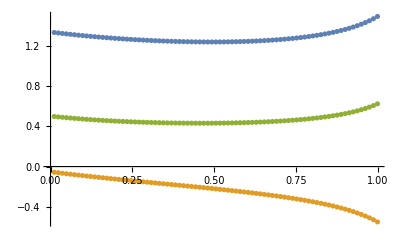

```mathematica
ListPlot[{Table[{i/Length[coefficientlist]-0.001,coefficientlist[[i]][[1]]},{i,1,Length[coefficientlist]}],Table[{i/Length[coefficientlist]-0.001,coefficientlist[[i]][[2]]},{i,1,Length[coefficientlist]}],Table[{i/Length[coefficientlist]-0.001,coefficientlist[[i]][[3]]},{i,1,Length[coefficientlist]}]}]
```

```mathematica
bstep=0.001;
cubicrenormalisationlist=Table[{b,1/(π^2)*NIntegrate[(1-ω[x,y,b]-γ[x,y]^2-γ[x,y]*(1-b^2))/(2ω[x,y,b]),{x,0,π},{y,0,π},MaxRecursion->100000,MinRecursion->90000,AccuracyGoal->10]},{b,0,1,bstep}];
```

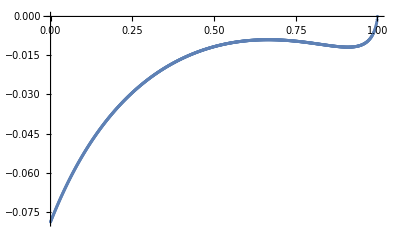

```mathematica
ListPlot[cubicrenormalisationlist]
```

```mathematica
Export["cantinganglerenormalisation.dat",cubicrenormalisationlist,"Data"];
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

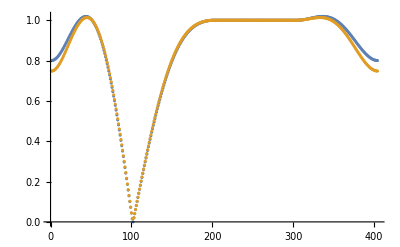

```mathematica
NNiklas=2^5;
renomlist={};
unrenomlist={};
AppendTo[unrenomlist,Table[ω[kx,kx,cubicrenormalisationlist[[i]][[1]]],{kx,0,π,1/NNiklas}]];
AppendTo[unrenomlist,Table[ω[π-kx,π,cubicrenormalisationlist[[i]][[1]]],{kx,0,π,1/NNiklas}]];
AppendTo[unrenomlist,Table[ω[kx,π-kx,cubicrenormalisationlist[[i]][[1]]],{kx,0,π,1/NNiklas}]];
AppendTo[unrenomlist,Table[ω[π-kx,0,cubicrenormalisationlist[[i]][[1]]],{kx,0,π,1/NNiklas}]];
AppendTo[renomlist,Table[ω[kx,kx,cubicrenormalisationlist[[i]][[1]]]+(1+γ[kx,kx])*(8cubicrenormalisationlist[[i]][[2]])*γ[kx,kx]*(cubicrenormalisationlist[[i]][[1]])^2/ω[kx,kx,cubicrenormalisationlist[[i]][[1]]],{kx,0,π,1/NNiklas}]];
AppendTo[renomlist,Table[ω[π-kx,π,cubicrenormalisationlist[[i]][[1]]]+(1+γ[π-kx,π])*(8*cubicrenormalisationlist[[i]][[2]])*γ[π-kx,π]*(cubicrenormalisationlist[[i]][[1]])^2/ω[π-kx,π,cubicrenormalisationlist[[i]][[1]]],{kx,0,π,1/NNiklas}]];
AppendTo[renomlist,Table[ω[kx,π-kx,cubicrenormalisationlist[[i]][[1]]]+(1+γ[kx,π-kx])*(8*cubicrenormalisationlist[[i]][[2]]*γ[kx,π-kx]*(cubicrenormalisationlist[[i]][[1]])^2)/ω[kx,π-kx,cubicrenormalisationlist[[i]][[1]]],{kx,0,π,1/NNiklas}]];
AppendTo[renomlist,Table[ω[π-kx,0,cubicrenormalisationlist[[i]][[1]]]+(1+γ[π-kx,0])*(8cubicrenormalisationlist[[i]][[2]])*γ[π-kx,0]*(cubicrenormalisationlist[[i]][[1]])^2/ω[π-kx,0,cubicrenormalisationlist[[i]][[1]]],{kx,0,π,1/NNiklas}]];
ListPlot[{Flatten[unrenomlist],Flatten[renomlist]}]
```

```mathematica
cubicrenormalisationlist[[4]]
```

{0.3,-0.0240351}

```mathematica
For[i=1,i<12,i++,
unrenomlist={};
NNiklas=2^ 7;
AppendTo[unrenomlist,Table[{kx*Sqrt[2],ω[kx,kx,cubicrenormalisationlist[[i]][[1]]],ω[kx,kx,cubicrenormalisationlist[[i]][[1]]]+(1+γ[kx,kx])*(8cubicrenormalisationlist[[i]][[2]])*γ[kx,kx]*(cubicrenormalisationlist[[i]][[1]])^2/ω[kx,kx,cubicrenormalisationlist[[i]][[1]]]},{kx,0,π,1/NNiklas}]];
AppendTo[unrenomlist,Table[{Sqrt[2]π+kx,ω[π-kx,π,cubicrenormalisationlist[[i]][[1]]],ω[π-kx,π,cubicrenormalisationlist[[i]][[1]]]+(1+γ[π-kx,π])*(8*cubicrenormalisationlist[[i]][[2]])*γ[π-kx,π]*(cubicrenormalisationlist[[i]][[1]])^2/ω[π-kx,π,cubicrenormalisationlist[[i]][[1]]]},{kx,0,π,1/NNiklas}]];
AppendTo[unrenomlist,Table[{(Sqrt[2]+1)π+Sqrt[2]*kx,ω[kx,π-kx,cubicrenormalisationlist[[i]][[1]]],ω[kx,π-kx,cubicrenormalisationlist[[i]][[1]]]+(1+γ[kx,π-kx])*(8*cubicrenormalisationlist[[i]][[2]]*γ[kx,π-kx]*(cubicrenormalisationlist[[i]][[1]])^2)/ω[kx,π-kx,cubicrenormalisationlist[[i]][[1]]]},{kx,0,π,1/NNiklas}]];
AppendTo[unrenomlist,Table[{(2*Sqrt[2]+1)π+kx,ω[π-kx,0,cubicrenormalisationlist[[i]][[1]]],ω[π-kx,0,cubicrenormalisationlist[[i]][[1]]]+(1+γ[π-kx,0])*(8cubicrenormalisationlist[[i]][[2]])*γ[π-kx,0]*(cubicrenormalisationlist[[i]][[1]])^2/ω[π-kx,0,cubicrenormalisationlist[[i]][[1]]]},{kx,0,π,1/NNiklas}]];
PlotList={Table[{Flatten[unrenomlist,1][[i]][[1]],Flatten[unrenomlist,1][[i]][[2]]},{i,1,Length[Flatten[unrenomlist,1]]}],Table[{Flatten[unrenomlist,1][[i]][[1]],Flatten[unrenomlist,1][[i]][[3]]},{i,1,Length[Flatten[unrenomlist,1]]}]};
(*ListLinePlot[PlotList]*)
ExportList=Table[{N[Flatten[unrenomlist,1][[i]][[1]]],Flatten[unrenomlist,1][[i]][[2]],Flatten[unrenomlist,1][[i]][[3]]},{i,1,Length[Flatten[unrenomlist,1]]}];
Export["frequencyindependentenergyrenormalisationB"<>ToString[(i-1)*10]<>"cBs.dat",N[ExportList],"Data"]];
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.